## Ventana Gaussiana

#### Ventana parabólica - ángulo θ

Ecuación correspondiente al ancho de la ventana de las curvas gaussianas para la estimación del ángulo θ de la matriz de transformación.

```mathematica
Clear[a,b]
Par[x_]=a x^2+b;(*Función parabólica*)
p1=π/8;(*Punto inferior para x=5000*)
p2 =π/4;(*Punto inferior para x=1*)
```

```mathematica
pars=Solve[Par[1]-p2==0&&Par[5000]-p1==0,{a,b}];
```

```mathematica
{a}=pars[[All,1,2]];
{b}=pars[[All,2,2]];
```

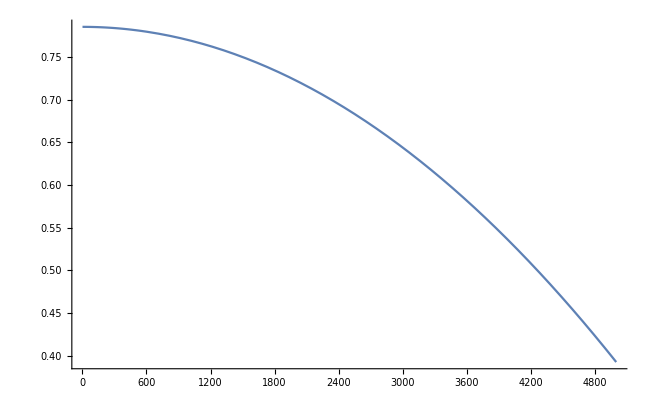

```mathematica
fp[x_]=(a)(x^2) + b;
Plot[fp[x],{x,1,5000}]
```

```mathematica
{a,b}(*Parámetros de la parábola*)
```

{-π/199999992,(49999999 π)/199999992}

#### Ventana parabólica - pixels (tx,ty)

Ecuación correspondiente al ancho de la ventana de las curvas gaussianas para la estimación de los parámetros tx y ty de la matriz de transformación.

```mathematica
Clear[a,b]
Par[x_]=a x^2+b;(*Función parabólica*)
p1=1;(*Punto inferior para x=5000*)
p2 =2;(*Punto inferior para x=1*)
```

```mathematica
pars=Solve[Par[1]-p2==0&&Par[5000]-p1==0,{a,b}];
```

```mathematica
{a}=pars[[All,1,2]];
{b}=pars[[All,2,2]];
```

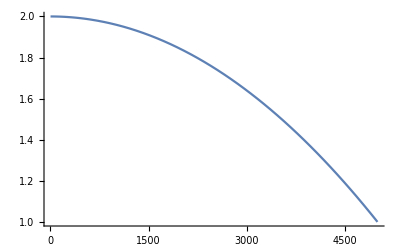

```mathematica
fp[x_]=(a)(x^2) + b;
Plot[fp[x],{x,1,5000}]
```

```mathematica
{a,b}(*Parámetros de la parábola*)
```

{-1/24999999,49999999/24999999}